# Omicron analysis: Plotting partitioned case counts and Rt

## Splitting out lineage BA.1 / clade 21K from lineage BA.2 / clade 21L

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-us-split

```mathematica
dataset="omicron-us-split";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

```mathematica
gridCount=4;
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron 21K","Omicron 21L"};
```

```mathematica
n=Length[variants]
```

4

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.7,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8083415999999999, 0.7110806000000001, 0.255976],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01","2022-03-01","2022-04-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

### Countries

```mathematica
countriesToDrop={};
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-11-01

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2022-03-04

```mathematica
countries=Union[seqData[[All,2]]]
```

{California,Colorado,Connecticut,Florida,Georgia,Illinois,Indiana,Maryland,Massachusetts,Michigan,Minnesota,Nevada,New Jersey,New York,North Carolina,Ohio,Oregon,Pennsylvania,Rhode Island,Tennessee,Texas,Utah,Virginia,Washington,Wisconsin}

```mathematica
countries=Complement[countries,countriesToDrop]
```

{California,Colorado,Connecticut,Florida,Georgia,Illinois,Indiana,Maryland,Massachusetts,Michigan,Minnesota,Nevada,New Jersey,New York,North Carolina,Ohio,Oregon,Pennsylvania,Rhode Island,Tennessee,Texas,Utah,Virginia,Washington,Wisconsin}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countryVariantCounts[country_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==country&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
countrySequenceCounts[country_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==country][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->countrySequenceCounts[#][[-15;;-1]]&,countries]
```

{California→{{2022-02-18,992},{2022-02-19,766},{2022-02-20,440},{2022-02-21,561},{2022-02-22,2066},{2022-02-23,587},{2022-02-24,450},{2022-02-25,345},{2022-02-26,172},{2022-02-27,79},{2022-02-28,157},{2022-03-01,617},{2022-03-02,3},{2022-03-03,2},{2022-03-04,0}},Colorado→{{2022-02-18,268},{2022-02-19,232},{2022-02-20,86},{2022-02-21,236},{2022-02-22,165},{2022-02-23,135},{2022-02-24,109},{2022-02-25,83},{2022-02-26,45},{2022-02-27,24},{2022-02-28,34},{2022-03-01,21},{2022-03-02,0},{2022-03-03,0},{2022-03-04,0}},Connecticut→{{2022-02-18,145},{2022-02-19,57},{2022-02-20,71},{2022-02-21,190},{2022-02-22,122},{2022-02-23,60},{2022-02-24,84},{2022-02-25,50},{2022-02-26,21},{2022-02-27,12},{2022-02-28,41},{2022-03-01,31},{2022-03-02,24},{2022-03-03,9},{2022-03-04,5}},Florida→{{2022-02-18,344},{2022-02-19,196},{2022-02-20,111},{2022-02-21,121},{2022-02-22,306},{2022-02-23,196},{2022-02-24,195},{2022-02-25,176},{2022-02-26,48},{2022-02-27,38},{2022-02-28,46},{2022-03-01,26},{2022-03-02,0},{2022-03-03,0},{2022-03-04,0}},Georgia→{{2022-02-18,78},{2022-02-19,70},{2022-02-20,30},{2022-02-21,45},{2022-02-22,43},{2022-02-23,50},{2022-02-24,45},{2022-02-25,49},{2022-02-26,12},{2022-02-27,6},{2022-02-28,10},{2022-03-01,11},{2022-03-02,0},{2022-03-03,0},{2022-03-04,0}},Illinois→{{2022-02-18,103},{2022-02-19,85},{2022-02-20,80},{2022-02-21,128},{2022-02-22,88},{2022-02-23,76},{2022-02-24,70},{2022-02-25,56},{2022-02-26,41},{2022-02-27,47},{2022-02-28,50},{2022-03-01,39},{2022-03-02,6},{2022-03-03,8},{2022-03-04,8}},Indiana→{{2022-02-18,54},{2022-02-19,44},{2022-02-20,16},{2022-02-21,49},{2022-02-22,64},{2022-02-23,23},{2022-02-24,30},{2022-02-25,32},{2022-02-26,3},{2022-02-27,4},{2022-02-28,3},{2022-03-01,0},{2022-03-02,0},{2022-03-03,0},{2022-03-04,0}},Maryland→{{2022-02-18,54},{2022-02-19,28},{2022-02-20,50},{2022-02-21,49},{2022-02-22,44},{2022-02-23,32},{2022-02-24,30},{2022-02-25,24},{2022-02-26,12},{2022-02-27,9},{2022-02-28,11},{2022-03-01,4},{2022-03-02,2},{2022-03-03,1},{2022-03-04,0}},Massachusetts→{{2022-02-18,318},{2022-02-19,173},{2022-02-20,188},{2022-02-21,288},{2022-02-22,382},{2022-02-23,327},{2022-02-24,291},{2022-02-25,78},{2022-02-26,152},{2022-02-27,142},{2022-02-28,315},{2022-03-01,221},{2022-03-02,182},{2022-03-03,53},{2022-03-04,0}},Michigan→{{2022-02-18,104},{2022-02-19,91},{2022-02-20,40},{2022-02-21,71},{2022-02-22,101},{2022-02-23,79},{2022-02-24,61},{2022-02-25,49},{2022-02-26,18},{2022-02-27,17},{2022-02-28,25},{2022-03-01,22},{2022-03-02,0},{2022-03-03,0},{2022-03-04,0}},Minnesota→{{2022-02-18,139},{2022-02-19,70},{2022-02-20,71},{2022-02-21,83},{2022-02-22,78},{2022-02-23,68},{2022-02-24,79},{2022-02-25,71},{2022-02-26,30},{2022-02-27,17},{2022-02-28,17},{2022-03-01,16},{2022-03-02,9},{2022-03-03,0},{2022-03-04,2}},Nevada→{{2022-02-18,30},{2022-02-19,30},{2022-02-20,27},{2022-02-21,69},{2022-02-22,25},{2022-02-23,27},{2022-02-24,40},{2022-02-25,37},{2022-02-26,33},{2022-02-27,7},{2022-02-28,20},{2022-03-01,3},{2022-03-02,1},{2022-03-03,3},{2022-03-04,5}},New Jersey→{{2022-02-18,114},{2022-02-19,93},{2022-02-20,61},{2022-02-21,108},{2022-02-22,95},{2022-02-23,76},{2022-02-24,61},{2022-02-25,18},{2022-02-26,22},{2022-02-27,9},{2022-02-28,21},{2022-03-01,16},{2022-03-02,2},{2022-03-03,0},{2022-03-04,0}},New York→{{2022-02-18,205},{2022-02-19,107},{2022-02-20,127},{2022-02-21,213},{2022-02-22,127},{2022-02-23,182},{2022-02-24,105},{2022-02-25,59},{2022-02-26,57},{2022-02-27,62},{2022-02-28,76},{2022-03-01,59},{2022-03-02,21},{2022-03-03,0},{2022-03-04,0}},North Carolina→{{2022-02-18,130},{2022-02-19,85},{2022-02-20,107},{2022-02-21,214},{2022-02-22,136},{2022-02-23,87},{2022-02-24,43},{2022-02-25,60},{2022-02-26,19},{2022-02-27,19},{2022-02-28,32},{2022-03-01,25},{2022-03-02,7},{2022-03-03,0},{2022-03-04,0}},Ohio→{{2022-02-18,69},{2022-02-19,68},{2022-02-20,18},{2022-02-21,45},{2022-02-22,44},{2022-02-23,38},{2022-02-24,22},{2022-02-25,35},{2022-02-26,11},{2022-02-27,16},{2022-02-28,16},{2022-03-01,4},{2022-03-02,0},{2022-03-03,0},{2022-03-04,0}},Oregon→{{2022-02-18,53},{2022-02-19,27},{2022-02-20,25},{2022-02-21,81},{2022-02-22,56},{2022-02-23,45},{2022-02-24,30},{2022-02-25,26},{2022-02-26,11},{2022-02-27,10},{2022-02-28,20},{2022-03-01,10},{2022-03-02,7},{2022-03-03,0},{2022-03-04,0}},Pennsylvania→{{2022-02-18,158},{2022-02-19,116},{2022-02-20,72},{2022-02-21,97},{2022-02-22,128},{2022-02-23,113},{2022-02-24,102},{2022-02-25,75},{2022-02-26,22},{2022-02-27,12},{2022-02-28,11},{2022-03-01,10},{2022-03-02,0},{2022-03-03,0},{2022-03-04,0}},Rhode Island→{{2022-02-18,32},{2022-02-19,8},{2022-02-20,18},{2022-02-21,42},{2022-02-22,32},{2022-02-23,46},{2022-02-24,15},{2022-02-25,10},{2022-02-26,2},{2022-02-27,9},{2022-02-28,12},{2022-03-01,14},{2022-03-02,6},{2022-03-03,0},{2022-03-04,0}},Tennessee→{{2022-02-18,65},{2022-02-19,42},{2022-02-20,40},{2022-02-21,31},{2022-02-22,71},{2022-02-23,46},{2022-02-24,44},{2022-02-25,30},{2022-02-26,6},{2022-02-27,14},{2022-02-28,11},{2022-03-01,9},{2022-03-02,7},{2022-03-03,0},{2022-03-04,0}},Texas→{{2022-02-18,343},{2022-02-19,156},{2022-02-20,172},{2022-02-21,294},{2022-02-22,183},{2022-02-23,158},{2022-02-24,121},{2022-02-25,132},{2022-02-26,67},{2022-02-27,52},{2022-02-28,105},{2022-03-01,85},{2022-03-02,51},{2022-03-03,0},{2022-03-04,0}},Utah→{{2022-02-18,126},{2022-02-19,58},{2022-02-20,62},{2022-02-21,147},{2022-02-22,62},{2022-02-23,91},{2022-02-24,29},{2022-02-25,32},{2022-02-26,9},{2022-02-27,4},{2022-02-28,65},{2022-03-01,28},{2022-03-02,0},{2022-03-03,0},{2022-03-04,0}},Virginia→{{2022-02-18,85},{2022-02-19,23},{2022-02-20,53},{2022-02-21,73},{2022-02-22,67},{2022-02-23,53},{2022-02-24,55},{2022-02-25,53},{2022-02-26,21},{2022-02-27,5},{2022-02-28,8},{2022-03-01,7},{2022-03-02,0},{2022-03-03,0},{2022-03-04,0}},Washington→{{2022-02-18,133},{2022-02-19,74},{2022-02-20,52},{2022-02-21,201},{2022-02-22,160},{2022-02-23,130},{2022-02-24,84},{2022-02-25,60},{2022-02-26,44},{2022-02-27,5},{2022-02-28,19},{2022-03-01,7},{2022-03-02,0},{2022-03-03,0},{2022-03-04,0}},Wisconsin→{{2022-02-18,102},{2022-02-19,46},{2022-02-20,48},{2022-02-21,65},{2022-02-22,55},{2022-02-23,89},{2022-02-24,60},{2022-02-25,50},{2022-02-26,27},{2022-02-27,14},{2022-02-28,12},{2022-03-01,17},{2022-03-02,0},{2022-03-03,0},{2022-03-04,0}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[country_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==country,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=15;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.00001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[4]]],PlotRange->{logitTransform[0.0005],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[4]]],PlotRange->{0,If[maxFreq>0.95,1,maxFreq]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[country_]:=Map[logisticPrevSeries[countryVariantCounts[country,#],countrySequenceCounts[country]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForCountries=Map[freqForCountry,countries];
```

```mathematica
modeledFreqsForCountries=Map[{modeledLogisticPrevSeries[logisticPrevSeries[countryVariantCounts[#,"Omicron 21L"],countrySequenceCounts[#]]]}&,countries];
```

```mathematica
legendsForCountries=Map[constructGrowthRateLegend[modeledGrowthRate[#[[4]]],variants[[4]],legendStartingPointY- 0.09,colors[[4]]]&,freqsForCountries];
```

```mathematica
panels=MapThread[logisticFreqPlotMultipleLineages,{freqsForCountries,modeledFreqsForCountries,legendsForCountries,countries}];
```

```mathematica
figLogistic=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis.png",figLogistic,"PNG",ImageResolution->300]
```

figures/omicron-us-split_logistic-growth-transformed-axis.png

```mathematica
panels=MapThread[naturalFreqPlotMultipleLineages,{freqsForCountries,modeledFreqsForCountries,legendsForCountries,countries}];
```

```mathematica
figNatural=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-natural-axis.png",figNatural,"PNG",ImageResolution->300]
```

figures/omicron-us-split_logistic-growth-natural-axis.png

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[country_,variant_]:=Module[{countryVariantFrequencyDateSeries,countryCasesDateSeries,tuples},
countryVariantFrequencyDateSeries=smoothedPrevalence[countryVariantCounts[country,variant],countrySequenceCounts[country]];
countryCasesDateSeries=csGather[country];
tuples=compareWithDate[countryVariantFrequencyDateSeries,countryCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
panels=Map[splitCasePlot,countries];
```

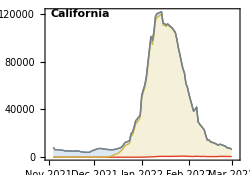
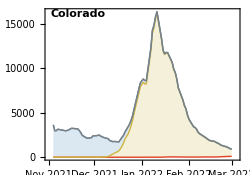
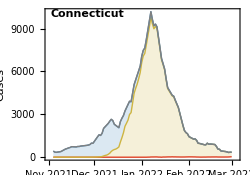
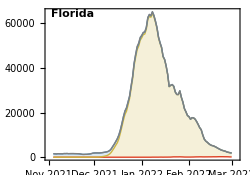
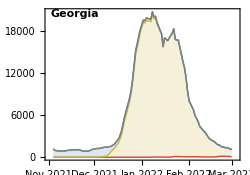
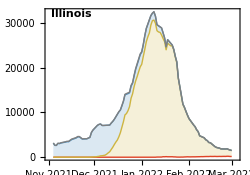
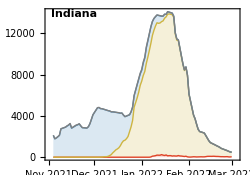
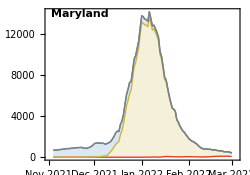
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us-split_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=500000;
```

```mathematica
splitCaseLogPlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{50,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[country_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{50,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[country_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[country,"Omicron 21L"];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->200,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{50,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[4]],FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.88,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
legendsForCountries=Map[constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather[#,"Omicron 21L"]],"Omicron 21L",legendStartingPointY- 0.09,colors[[4]]]&,countries];
```

```mathematica
panels=MapThread[Show[splitCaseLogPlot[#1,#2],splitCaseLogPlotModeledOmicron[#1]]&,{countries,legendsForCountries}];
```

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us-split_partitioned-log-cases.png